```mathematica
G=Graph[{1<->2,2<->3,3<->1,1<->4,4<->2},VertexLabels->"Name",EdgeWeight->{1,2,2,0.5,0.5}]
```

-Graphics-

```mathematica
GraphPlot3D[G]
```

-Graphics3D-

```mathematica
GraphPlot3D[G, EdgeRenderingFunction->({Cylinder[#1, .05]}&), VertexRenderingFunction->({Sphere[#, 0.1]}&)]
```

-Graphics3D-

```mathematica
PropertyValue[{G,#}, VertexCoordinates] & /@ VertexList[G]
```

{{0.933811,0.869483},{0.934118,0.},{0.,0.435027},{1.86762,0.43517}}

```mathematica
H=Graph[{1<->2,1<->3,1<->4,2<->3, 2<->4, 3<->4},VertexLabels->"Name",EdgeWeight->{4,3,5,5,3,4}]
```

-Graphics-

```mathematica
xH = {{0,0}, {4,0}, {0,3}, {4,3}}
```

{{0,0},{4,0},{0,3},{4,3}}

```mathematica
RigidityMatrix[g_Graph,x_List?MatrixQ]:=Block[{K=Dimensions[x][[2]],n=Dimensions[x][[1]],EL=EdgeList[G],m,R,ed,secant},m=Length[EL];
R=ConstantArray[0,{m,n K}];
For[i=1,i≤m,i++,ed=EL[[i]];
For[j=1,j≤n,j++,If[j==ed[[1]],secant=x[[j]]-x[[ed[[2]]]],If[j==ed[[2]],secant=x[[j]]-x[[ed[[1]]]],secant=ConstantArray[0,K]]];
For[k=1,k≤K,k++,R[[i,K (j-1)+k]]=secant[[k]]]]];
Return[R];]
```

```mathematica
RH = RigidityMatrix[H,xH]
```

{{-4,0,4,0,0,0,0,0},{0,0,4,-3,-4,3,0,0},{0,-3,0,0,0,3,0,0},{-4,-3,0,0,0,0,4,3},{0,0,0,-3,0,0,0,3}}

```mathematica
MatrixRank[RH]
```

5

```mathematica
xHpartial = xH[[1;;3]]
```

{{0,0},{4,0},{0,3}}

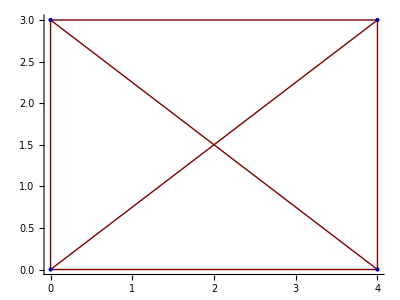

```mathematica
GraphPlot[H, VertexCoordinateRules -> xH, Axes -> True]
```

```mathematica
y = {y1, y2}
```

{y1,y2}

```mathematica
Norm[y]
```

√(Abs[y1]^2+Abs[y2]^2)

```mathematica
NormSquared[y_List] := (Norm[y])^2
```

```mathematica
NormSquared[y]
```

Abs[y1]^2+Abs[y2]^2

```mathematica
DGPSystem[G_Graph, K_Integer] := Block[{x}, x = ConstantArray[0, {Length[VertexList[G]], K}];Map[(NormSquared[x[[#[[1]]]]-x[[#[[2]]]]== (WeightedAdjacencyMatrix[G][[#[[1]],#[[2]]]])^2)&, EdgeList[G]]]
```

```mathematica
DGPSystem[H, 2]
```

DGPSystem[-Graphics-,2]

```mathematica
X = Array[Array[x,3],2]
```

{{x[1],x[2],x[3]}[1],{x[1],x[2],x[3]}[2]}

```mathematica
x[1]=2
```

2

```mathematica
x[1][2] = 3
```

3

```mathematica
x[1][2]
```

3

```mathematica
X[[1,2]]
```

{{x[1],x[2],x[3]}[1],{x[1],x[2],x[3]}[2]}⟦1,2⟧

```mathematica
ClearAll["x", "X"]
```

```mathematica
y = Array[x, {3,2}]
```

{{x[1,1],x[1,2]},{x[2,1],x[2,2]},{x[3,1],x[3,2]}}

```mathematica
y[[2,1]]
```

x[2,1]

```mathematica
y[[2]]
```

{x[2,1],x[2,2]}

```mathematica
DGPSystemSquared[G_Graph,K_Integer]:=Block[{x,theSystem},x=Array[y,{Length[VertexList[G]],K}];
theSystem=Map[(Sum[(x[[#[[1]],k]]-x[[#[[2]],k]])^2,{k,K}]==(WeightedAdjacencyMatrix[G][[#[[1]],#[[2]]]])^2)&,EdgeList[G]]]
```

```mathematica
DGPSystemSquared[G, 2]
```

{({{{«1»,{x[2,1],x[2,2]},{x[3,1],x[3,2]}}[1,1],«1»},{«1»[2,1],{«1»}[2,2]},{{«1»}[3,1],«1»},«1»}⟦1,3⟧-«1»)^2+(«1»)^2==1,(-x⟦3,3⟧+{«1»}⟦2,3⟧)^2+({«1»}⟦2,3⟧-«1»)^2==4,«1»,(«1»)^2+((«1»«1»)^2==0.25,(-x⟦2,3⟧+«1»)^2+(-«1»⟦2,3⟧+{«1»}⟦4,3⟧)^2==0.25}

```mathematica
ClearAll["X", "x", "y"]
```

```mathematica
DGPSystem[G_Graph,K_Integer]:=Block[{x,y,theSystem},x=Array[y,{Length[VertexList[G]],K}];
theSystem=Map[(Sqrt[Sum[(x[[#[[1]],k]]-x[[#[[2]],k]])^2,{k,K}]]==WeightedAdjacencyMatrix[G][[#[[1]],#[[2]]]])&,EdgeList[G]];
Return[theSystem]]
```

```mathematica
S = DGPSystemSquared[G, 2]
```

{(y[1,1]-y[2,1])^2+(y[1,2]-y[2,2])^2==1,(y[2,1]-y[3,1])^2+(y[2,2]-y[3,2])^2==4,(-y[1,1]+y[3,1])^2+(-y[1,2]+y[3,2])^2==4,(y[1,1]-y[4,1])^2+(y[1,2]-y[4,2])^2==0.25,(-y[2,1]+y[4,1])^2+(-y[2,2]+y[4,2])^2==0.25}

```mathematica
Solve[%114,{y[1,1],y[1,2],y[2,1],y[2,2],y[3,1],y[3,2],y[4,1],y[4,2]}]
```

{{y[2,1]→y[1,1]-1. √(1.-1. y[1,2]^2+2. y[1,2] y[2,2]-1. y[2,2]^2),y[3,1]→0.5 (2. y[1,1]-1. √(1.-1. y[1,2]^2+2. y[1,2] y[2,2]-1. y[2,2]^2)-1. √(15. y[1,2]^2-30. y[1,2] y[2,2]+15. y[2,2]^2)),y[3,2]→(0.5 (y[1,2]^2-1. y[2,2]^2+3.87298 √((y[1,2]-1. y[2,2])^2) √(1.-1. y[1,2]^2+2. y[1,2] y[2,2]-1. y[2,2]^2)))/(y[1,2]-1. y[2,2]),y[4,1]→0.5 (2. y[1,1]-1. √(1.-1. y[1,2]^2+2. y[1,2] y[2,2]-1. y[2,2]^2)),y[4,2]→0.5 (y[1,2]+y[2,2])},{y[2,1]→y[1,1]-1. √(1.-1. y[1,2]^2+2. y[1,2] y[2,2]-1. y[2,2]^2),y[3,1]→0.5 (2. y[1,1]-1. √(1.-1. y[1,2]^2+2. y[1,2] y[2,2]-1. y[2,2]^2)+√(15. y[1,2]^2-30. y[1,2] y[2,2]+15. y[2,2]^2)),y[3,2]→(0.5 (y[1,2]^2-1. y[2,2]^2-3.87298 √((y[1,2]-1. y[2,2])^2) √(1.-1. y[1,2]^2+2. y[1,2] y[2,2]-1. y[2,2]^2)))/(y[1,2]-1. y[2,2]),y[4,1]→0.5 (2. y[1,1]-1. √(1.-1. y[1,2]^2+2. y[1,2] y[2,2]-1. y[2,2]^2)),y[4,2]→0.5 (y[1,2]+y[2,2])},{y[2,1]→y[1,1]+√(1.-1. y[1,2]^2+2. y[1,2] y[2,2]-1. y[2,2]^2),y[3,1]→0.5 (2. y[1,1]+√(1.-1. y[1,2]^2+2. y[1,2] y[2,2]-1. y[2,2]^2)-1. √(15. y[1,2]^2-30. y[1,2] y[2,2]+15. y[2,2]^2)),y[3,2]→(0.5 (y[1,2]^2-1. y[2,2]^2-3.87298 √((y[1,2]-1. y[2,2])^2) √(1.-1. y[1,2]^2+2. y[1,2] y[2,2]-1. y[2,2]^2)))/(y[1,2]-1. y[2,2]),y[4,1]→0.5 (2. y[1,1]+√(1.-1. y[1,2]^2+2. y[1,2] y[2,2]-1. y[2,2]^2)),y[4,2]→0.5 (y[1,2]+y[2,2])},{y[2,1]→y[1,1]+√(1.-1. y[1,2]^2+2. y[1,2] y[2,2]-1. y[2,2]^2),y[3,1]→0.5 (2. y[1,1]+√(1.-1. y[1,2]^2+2. y[1,2] y[2,2]-1. y[2,2]^2)+√(15. y[1,2]^2-30. y[1,2] y[2,2]+15. y[2,2]^2)),y[3,2]→(0.5 (y[1,2]^2-1. y[2,2]^2+3.87298 √((y[1,2]-1. y[2,2])^2) √(1.-1. y[1,2]^2+2. y[1,2] y[2,2]-1. y[2,2]^2)))/(y[1,2]-1. y[2,2]),y[4,1]→0.5 (2. y[1,1]+√(1.-1. y[1,2]^2+2. y[1,2] y[2,2]-1. y[2,2]^2)),y[4,2]→0.5 (y[1,2]+y[2,2])},{y[2,1]→-1.+y[1,1],y[2,2]→y[1,2],y[3,1]→0.5 (-1.+2. y[1,1]),y[3,2]→0.5 (-3.87298+2. y[1,2]),y[4,1]→0.5 (-1.+2. y[1,1]),y[4,2]→y[1,2]},{y[2,1]→-1.+y[1,1],y[2,2]→y[1,2],y[3,1]→0.5 (-1.+2. y[1,1]),y[3,2]→0.5 (3.87298+2. y[1,2]),y[4,1]→0.5 (-1.+2. y[1,1]),y[4,2]→y[1,2]},{y[2,1]→1.+y[1,1],y[2,2]→y[1,2],y[3,1]→0.5 (1.+2. y[1,1]),y[3,2]→0.5 (-3.87298+2. y[1,2]),y[4,1]→0.5 (1.+2. y[1,1]),y[4,2]→y[1,2]},{y[2,1]→1.+y[1,1],y[2,2]→y[1,2],y[3,1]→0.5 (1.+2. y[1,1]),y[3,2]→0.5 (3.87298+2. y[1,2]),y[4,1]→0.5 (1.+2. y[1,1]),y[4,2]→y[1,2]}}

```mathematica
Solve[S, Flatten[Array[y, {4, 2}]]]
```

{{y[2,1]→y[1,1]-1. √(1.-1. y[1,2]^2+2. y[1,2] y[2,2]-1. y[2,2]^2),y[3,1]→0.5 (2. y[1,1]-1. √(1.-1. y[1,2]^2+2. y[1,2] y[2,2]-1. y[2,2]^2)-1. √(15. y[1,2]^2-30. y[1,2] y[2,2]+15. y[2,2]^2)),y[3,2]→(0.5 (y[1,2]^2-1. y[2,2]^2+3.87298 √((y[1,2]-1. y[2,2])^2) √(1.-1. y[1,2]^2+2. y[1,2] y[2,2]-1. y[2,2]^2)))/(y[1,2]-1. y[2,2]),y[4,1]→0.5 (2. y[1,1]-1. √(1.-1. y[1,2]^2+2. y[1,2] y[2,2]-1. y[2,2]^2)),y[4,2]→0.5 (y[1,2]+y[2,2])},{y[2,1]→y[1,1]-1. √(1.-1. y[1,2]^2+2. y[1,2] y[2,2]-1. y[2,2]^2),y[3,1]→0.5 (2. y[1,1]-1. √(1.-1. y[1,2]^2+2. y[1,2] y[2,2]-1. y[2,2]^2)+√(15. y[1,2]^2-30. y[1,2] y[2,2]+15. y[2,2]^2)),y[3,2]→(0.5 (y[1,2]^2-1. y[2,2]^2-3.87298 √((y[1,2]-1. y[2,2])^2) √(1.-1. y[1,2]^2+2. y[1,2] y[2,2]-1. y[2,2]^2)))/(y[1,2]-1. y[2,2]),y[4,1]→0.5 (2. y[1,1]-1. √(1.-1. y[1,2]^2+2. y[1,2] y[2,2]-1. y[2,2]^2)),y[4,2]→0.5 (y[1,2]+y[2,2])},{y[2,1]→y[1,1]+√(1.-1. y[1,2]^2+2. y[1,2] y[2,2]-1. y[2,2]^2),y[3,1]→0.5 (2. y[1,1]+√(1.-1. y[1,2]^2+2. y[1,2] y[2,2]-1. y[2,2]^2)-1. √(15. y[1,2]^2-30. y[1,2] y[2,2]+15. y[2,2]^2)),y[3,2]→(0.5 (y[1,2]^2-1. y[2,2]^2-3.87298 √((y[1,2]-1. y[2,2])^2) √(1.-1. y[1,2]^2+2. y[1,2] y[2,2]-1. y[2,2]^2)))/(y[1,2]-1. y[2,2]),y[4,1]→0.5 (2. y[1,1]+√(1.-1. y[1,2]^2+2. y[1,2] y[2,2]-1. y[2,2]^2)),y[4,2]→0.5 (y[1,2]+y[2,2])},{y[2,1]→y[1,1]+√(1.-1. y[1,2]^2+2. y[1,2] y[2,2]-1. y[2,2]^2),y[3,1]→0.5 (2. y[1,1]+√(1.-1. y[1,2]^2+2. y[1,2] y[2,2]-1. y[2,2]^2)+√(15. y[1,2]^2-30. y[1,2] y[2,2]+15. y[2,2]^2)),y[3,2]→(0.5 (y[1,2]^2-1. y[2,2]^2+3.87298 √((y[1,2]-1. y[2,2])^2) √(1.-1. y[1,2]^2+2. y[1,2] y[2,2]-1. y[2,2]^2)))/(y[1,2]-1. y[2,2]),y[4,1]→0.5 (2. y[1,1]+√(1.-1. y[1,2]^2+2. y[1,2] y[2,2]-1. y[2,2]^2)),y[4,2]→0.5 (y[1,2]+y[2,2])},{y[2,1]→-1.+y[1,1],y[2,2]→y[1,2],y[3,1]→0.5 (-1.+2. y[1,1]),y[3,2]→0.5 (-3.87298+2. y[1,2]),y[4,1]→0.5 (-1.+2. y[1,1]),y[4,2]→y[1,2]},{y[2,1]→-1.+y[1,1],y[2,2]→y[1,2],y[3,1]→0.5 (-1.+2. y[1,1]),y[3,2]→0.5 (3.87298+2. y[1,2]),y[4,1]→0.5 (-1.+2. y[1,1]),y[4,2]→y[1,2]},{y[2,1]→1.+y[1,1],y[2,2]→y[1,2],y[3,1]→0.5 (1.+2. y[1,1]),y[3,2]→0.5 (-3.87298+2. y[1,2]),y[4,1]→0.5 (1.+2. y[1,1]),y[4,2]→y[1,2]},{y[2,1]→1.+y[1,1],y[2,2]→y[1,2],y[3,1]→0.5 (1.+2. y[1,1]),y[3,2]→0.5 (3.87298+2. y[1,2]),y[4,1]→0.5 (1.+2. y[1,1]),y[4,2]→y[1,2]}}

```mathematica
y[1,1]
```

```mathematica
y[1,2]=0
```

0

```mathematica
y[4,2]
```

```mathematica
y[4,2]
```

y[4,2]

```mathematica
y[[4,2]]
```

y⟦4,2⟧

```mathematica
y[4]
```

y[4]

```mathematica
z=Array[v, {4,2}]
```

{{v[1,1],v[1,2]},{v[2,1],v[2,2]},{v[3,1],v[3,2]},{v[4,1],v[4,2]}}

```mathematica
DGPSystemSquaredVars[G_Graph,K_Integer,y_]:=Block[{theSystem},theSystem=Map[(Sum[(y[[#[[1]],k]]-y[[#[[2]],k]])^2,{k,K}]==(WeightedAdjacencyMatrix[G][[#[[1]],#[[2]]]])^2)&,EdgeList[G]];
Return[theSystem]]
```

```mathematica
S = DGPSystemSquaredVars[G, 2, z]
```

{(v[1,1]-v[2,1])^2+(v[1,2]-v[2,2])^2==1,(v[2,1]-v[3,1])^2+(v[2,2]-v[3,2])^2==4,(-v[1,1]+v[3,1])^2+(-v[1,2]+v[3,2])^2==4,(v[1,1]-v[4,1])^2+(v[1,2]-v[4,2])^2==0.25,(-v[2,1]+v[4,1])^2+(-v[2,2]+v[4,2])^2==0.25}

```mathematica
sol = Solve[Apply[And, S], Flatten[z], Reals]
```

{{v[2,2]→ConditionalExpression[v[1,2]-1. √(1.-1. v[1,1]^2+2. v[1,1] v[2,1]-1. v[2,1]^2),-1.+v[1,1]<v[2,1]<0.25 (-1.+4. v[1,1])],v[3,1]→ConditionalExpression[0.5 (v[1,1]+v[2,1])+1.93649 √(1.-1. v[1,1]^2+2. v[1,1] v[2,1]-1. v[2,1]^2),-1.+v[1,1]<v[2,1]<0.25 (-1.+4. v[1,1])],v[3,2]→«1»,v[4,1]→ConditionalExpression[0.5 (v[1,1]+v[2,1]),-1.+v[1,1]<v[2,1]<0.25 (-1.+4. v[1,1])],v[4,2]→ConditionalExpression[v[1,2]-1. √(1.-1. v[1,1]^2+2. v[1,1] v[2,1]-1. v[2,1]^2)+0.5 √(1.-4. v[2,1]^2+4. v[2,1] (v[1,1]+v[2,1])-1. (v[1,1]+v[2,1])^2),-1.+v[1,1]<v[2,1]<0.25 (-1.+4. v[1,1])]},«18»,{v[2,1]→0.25 (1.+4. v[1,1]),«4»,v[4,2]→√(1.-1. v[1,1]^2+0.5 v[1,1] (1.+4. v[1,1])-0.0625 (1.+4. v[1,1])^2)-0.5 √(1.-0.25 (1.+4. v[1,1])^2+1. (1.+4. v[1,1]) (v[1,1]+0.25 (1.+4. v[1,1]))-1. (v[1,1]+0.25 (1.+4. v[1,1]))^2)+v[1,2]}}

```mathematica
sol /. {v[1,1] -> 0, v[1,2]->0, v[2,1]=2, v[2,2]=0}
```

{{0→ConditionalExpression[-1. √(-3.+4. v[1,1]-1. v[1,1]^2)+v[1,2],v[1,1]<3.&&0.25-1. v[1,1]<-2],v[3,1]→ConditionalExpression[0.5 (2+v[1,1])+1.93649 √(-3.+4. v[1,1]-1. v[1,1]^2),v[1,1]<3.&&0.25-1. v[1,1]<-2],v[3,2]→ConditionalExpression[-1. √(-3.+4. v[1,1]-1. v[1,1]^2)-1. √(0.+4. (0.5 (2+v[1,1])+1.93649 √(-3.+4. v[1,1]-1. v[1,1]^2))-1. (0.5 (2+v[1,1])+1.93649 √(-3.+4. v[1,1]-1. v[1,1]^2))^2)+v[1,2],v[1,1]<3.&&0.25-1. v[1,1]<-2],v[4,1]→ConditionalExpression[0.5 (2+v[1,1]),v[1,1]<3.&&0.25-1. v[1,1]<-2],v[4,2]→ConditionalExpression[-1. √(-3.+4. v[1,1]-1. v[1,1]^2)+0.5 √(-15.+8. (2+v[1,1])-1. (2+v[1,1])^2)+v[1,2],v[1,1]<3.&&0.25-1. v[1,1]<-2]},«18»,{2→0.25 (1.+4. v[1,1]),«4»,v[4,2]→√(1.-1. v[1,1]^2+0.5 v[1,1] (1.+4. v[1,1])-0.0625 (1.+4. v[1,1])^2)-0.5 √(1.-0.25 (1.+«1»)^2+1. «1» (v[1,1]+«5» «1»)-1. (v[1,1]+0.25 (1.+«1»))^2)+v[1,2]}}«2»«1»{«1»}

```mathematica
(z /.sol)/.{v[1,1]->0, v[1,2]->0, v[2,1]->2}
```

{{{0,0},{2,Undefined},{Undefined,Undefined},{Undefined,Undefined}},{{0,0},{2,Undefined},{Undefined,Undefined},{Undefined,Undefined}},{{0,0},{2,Undefined},{Undefined,Undefined},{Undefined,Undefined}},{{0,0},{2,Undefined},{Undefined,Undefined},{Undefined,Undefined}},{{0,0},{2,Undefined},{Undefined,Undefined},{Undefined,Undefined}},{{0,0},{2,Undefined},{Undefined,Undefined},{Undefined,Undefined}},{{0,0},{2,Undefined},{Undefined,Undefined},{Undefined,Undefined}},{{0,0},{2,Undefined},{Undefined,Undefined},{Undefined,Undefined}},{{0,v[1,-1.]},{-1.,0.},{-0.5,-1.93649},{-0.5,0.}},{{0,v[1,-1.]},{-1.,0.},{-0.5,1.93649},{-0.5,0.}},{{0,v[1,1.]},{1.,0.},{0.5,-1.93649},{0.5,0.}},{{0,v[1,1.]},{1.,0.},{0.5,1.93649},{0.5,0.}},{{0,v[1,-0.25]},{-0.25,-0.968246},{-2.,0.},{-0.125,-0.484123}},{{0,v[1,-0.25]},{-0.25,-0.968246},{1.75,-0.968246-2.98023×10^-8 ⅈ},{-0.125,-0.484123}},{{0,v[1,-0.25]},{-0.25,0.968246},{-2.,0.},{-0.125,0.484123}},{{0,v[1,-0.25]},{-0.25,0.968246},{1.75,0.968246-2.98023×10^-8 ⅈ},{-0.125,0.484123}},{{0,v[1,0.25]},{0.25,-0.968246},{-1.75,-0.968246-2.98023×10^-8 ⅈ},{0.125,-0.484123}},{{0,v[1,0.25]},{0.25,-0.968246},{2.,0.},{0.125,-0.484123}},{{0,v[1,0.25]},{0.25,0.968246},{-1.75,0.968246-2.98023×10^-8 ⅈ},{0.125,0.484123}},{{0,v[1,0.25]},{0.25,0.968246},{2.,0.},{0.125,0.484123}}}

```mathematica
G=Graph[{1<->3,1<->4,2<->3, 2<->4},EdgeWeight->{2,1,2,1}, VertexLabels->"Name"]
```

-Graphics-

```mathematica
Get["~/maths/ibmer/papers/mdgp/intro_dg/DGPSystem.m"]
```

```mathematica
S = DGPSystemSquared[G,2]
```

{(y[1,1]-y[3,1])^2+(y[1,2]-y[3,2])^2==4,(y[1,1]-y[4,1])^2+(y[1,2]-y[4,2])^2==1,(y[2,1]-y[3,1])^2+(y[2,2]-y[3,2])^2==4,(y[2,1]-y[4,1])^2+(y[2,2]-y[4,2])^2==1}

```mathematica
Normal[WeightedAdjacencyMatrix[G]][[1,4]]
```

0

```mathematica
MatrixForm[Normal[WeightedAdjacencyMatrix[G]]]
```

(0 | 2 | 1 | 0
2 | 0 | 0 | 2
1 | 0 | 0 | 1
0 | 2 | 1 | 0)

```mathematica
EdgeList[G]
```

{1<->3,1<->4,2<->3,2<->4}

```mathematica
VertexList[G]
```

{1,3,4,2}

```mathematica
NoTranslations = Map[(y[1,#]-> 0)&, Range[2]]
```

{y[1,1]→0,y[1,2]→0}

```mathematica
SI = S /. NoTranslations
```

{y[3,1]^2+y[3,2]^2==4,y[4,1]^2+y[4,2]^2==1,(y[2,1]-y[3,1])^2+(y[2,2]-y[3,2])^2==4,(y[2,1]-y[4,1])^2+(y[2,2]-y[4,2])^2==1}

```mathematica
SIEq = Apply[And, SI]
```

y[3,1]^2+y[3,2]^2==4&&y[4,1]^2+y[4,2]^2==1&&(y[2,1]-y[3,1])^2+(y[2,2]-y[3,2])^2==4&&(y[2,1]-y[4,1])^2+(y[2,2]-y[4,2])^2==1

```mathematica
MyVars = Array[y, {4, 2}]
```

{{y[1,1],y[1,2]},{y[2,1],y[2,2]},{y[3,1],y[3,2]},{y[4,1],y[4,2]}}

```mathematica
VarList = Cases[(Flatten[MyVars] /. NoTranslations), Except[0]]
```

{y[2,1],y[2,2],y[3,1],y[3,2],y[4,1],y[4,2]}

```mathematica
Solve[SIEq, VarList]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{y[2,1]→0,y[2,2]→0,y[3,2]→-√(4-y[3,1]^2),y[4,2]→-√(1-y[4,1]^2)},{y[2,1]→0,y[2,2]→0,y[3,2]→-√(4-y[3,1]^2),y[4,2]→√(1-y[4,1]^2)},{y[2,1]→0,y[2,2]→0,y[3,2]→√(4-y[3,1]^2),y[4,2]→-√(1-y[4,1]^2)},{y[2,1]→0,y[2,2]→0,y[3,2]→√(4-y[3,1]^2),y[4,2]→√(1-y[4,1]^2)},{y[3,1]→(y[2,1]^3+y[2,1] y[2,2]^2-√(16 y[2,1]^2 y[2,2]^2-y[2,1]^4 y[2,2]^2+16 y[2,2]^4-2 y[2,1]^2 y[2,2]^4-y[2,2]^6))/(2 (y[2,1]^2+y[2,2]^2)),y[3,2]→(y[2,1]^2+y[2,2]^2-y[2,1]^4/(y[2,1]^2+y[2,2]^2)-(y[2,1]^2 y[2,2]^2)/(y[2,1]^2+y[2,2]^2)+(y[2,1] √(-y[2,2]^2 (-16 y[2,1]^2+y[2,1]^4-16 y[2,2]^2+2 y[2,1]^2 y[2,2]^2+y[2,2]^4)))/(y[2,1]^2+y[2,2]^2))/(2 y[2,2]),y[4,1]→(y[2,1]^3+y[2,1] y[2,2]^2-√(4 y[2,1]^2 y[2,2]^2-y[2,1]^4 y[2,2]^2+4 y[2,2]^4-2 y[2,1]^2 y[2,2]^4-y[2,2]^6))/(2 (y[2,1]^2+y[2,2]^2)),y[4,2]→(y[2,1]^2+y[2,2]^2-y[2,1]^4/(y[2,1]^2+y[2,2]^2)-(y[2,1]^2 y[2,2]^2)/(y[2,1]^2+y[2,2]^2)+(y[2,1] √(-y[2,2]^2 (-4 y[2,1]^2+y[2,1]^4-4 y[2,2]^2+2 y[2,1]^2 y[2,2]^2+y[2,2]^4)))/(y[2,1]^2+y[2,2]^2))/(2 y[2,2])},{y[3,1]→(y[2,1]^3+y[2,1] y[2,2]^2-√(16 y[2,1]^2 y[2,2]^2-y[2,1]^4 y[2,2]^2+16 y[2,2]^4-2 y[2,1]^2 y[2,2]^4-y[2,2]^6))/(2 (y[2,1]^2+y[2,2]^2)),y[3,2]→(y[2,1]^2+y[2,2]^2-y[2,1]^4/(y[2,1]^2+y[2,2]^2)-(y[2,1]^2 y[2,2]^2)/(y[2,1]^2+y[2,2]^2)+(y[2,1] √(-y[2,2]^2 (-16 y[2,1]^2+y[2,1]^4-16 y[2,2]^2+2 y[2,1]^2 y[2,2]^2+y[2,2]^4)))/(y[2,1]^2+y[2,2]^2))/(2 y[2,2]),y[4,1]→(y[2,1]^3+y[2,1] y[2,2]^2+√(4 y[2,1]^2 y[2,2]^2-y[2,1]^4 y[2,2]^2+4 y[2,2]^4-2 y[2,1]^2 y[2,2]^4-y[2,2]^6))/(2 (y[2,1]^2+y[2,2]^2)),y[4,2]→(y[2,1]^2+y[2,2]^2-y[2,1]^4/(y[2,1]^2+y[2,2]^2)-(y[2,1]^2 y[2,2]^2)/(y[2,1]^2+y[2,2]^2)-(y[2,1] √(-y[2,2]^2 (-4 y[2,1]^2+y[2,1]^4-4 y[2,2]^2+2 y[2,1]^2 y[2,2]^2+y[2,2]^4)))/(y[2,1]^2+y[2,2]^2))/(2 y[2,2])},{y[3,1]→(y[2,1]^3+y[2,1] y[2,2]^2+√(16 y[2,1]^2 y[2,2]^2-y[2,1]^4 y[2,2]^2+16 y[2,2]^4-2 y[2,1]^2 y[2,2]^4-y[2,2]^6))/(2 (y[2,1]^2+y[2,2]^2)),y[3,2]→(y[2,1]^2+y[2,2]^2-y[2,1]^4/(y[2,1]^2+y[2,2]^2)-(y[2,1]^2 y[2,2]^2)/(y[2,1]^2+y[2,2]^2)-(y[2,1] √(-y[2,2]^2 (-16 y[2,1]^2+y[2,1]^4-16 y[2,2]^2+2 y[2,1]^2 y[2,2]^2+y[2,2]^4)))/(y[2,1]^2+y[2,2]^2))/(2 y[2,2]),y[4,1]→(y[2,1]^3+y[2,1] y[2,2]^2-√(4 y[2,1]^2 y[2,2]^2-y[2,1]^4 y[2,2]^2+4 y[2,2]^4-2 y[2,1]^2 y[2,2]^4-y[2,2]^6))/(2 (y[2,1]^2+y[2,2]^2)),y[4,2]→(y[2,1]^2+y[2,2]^2-y[2,1]^4/(y[2,1]^2+y[2,2]^2)-(y[2,1]^2 y[2,2]^2)/(y[2,1]^2+y[2,2]^2)+(y[2,1] √(-y[2,2]^2 (-4 y[2,1]^2+y[2,1]^4-4 y[2,2]^2+2 y[2,1]^2 y[2,2]^2+y[2,2]^4)))/(y[2,1]^2+y[2,2]^2))/(2 y[2,2])},{y[3,1]→(y[2,1]^3+y[2,1] y[2,2]^2+√(16 y[2,1]^2 y[2,2]^2-y[2,1]^4 y[2,2]^2+16 y[2,2]^4-2 y[2,1]^2 y[2,2]^4-y[2,2]^6))/(2 (y[2,1]^2+y[2,2]^2)),y[3,2]→(y[2,1]^2+y[2,2]^2-y[2,1]^4/(y[2,1]^2+y[2,2]^2)-(y[2,1]^2 y[2,2]^2)/(y[2,1]^2+y[2,2]^2)-(y[2,1] √(-y[2,2]^2 (-16 y[2,1]^2+y[2,1]^4-16 y[2,2]^2+2 y[2,1]^2 y[2,2]^2+y[2,2]^4)))/(y[2,1]^2+y[2,2]^2))/(2 y[2,2]),y[4,1]→(y[2,1]^3+y[2,1] y[2,2]^2+√(4 y[2,1]^2 y[2,2]^2-y[2,1]^4 y[2,2]^2+4 y[2,2]^4-2 y[2,1]^2 y[2,2]^4-y[2,2]^6))/(2 (y[2,1]^2+y[2,2]^2)),y[4,2]→(y[2,1]^2+y[2,2]^2-y[2,1]^4/(y[2,1]^2+y[2,2]^2)-(y[2,1]^2 y[2,2]^2)/(y[2,1]^2+y[2,2]^2)-(y[2,1] √(-y[2,2]^2 (-4 y[2,1]^2+y[2,1]^4-4 y[2,2]^2+2 y[2,1]^2 y[2,2]^2+y[2,2]^4)))/(y[2,1]^2+y[2,2]^2))/(2 y[2,2])},{y[2,1]→0,y[3,1]→-1/2 √(16-y[2,2]^2),y[3,2]→1/2 y[2,2],y[4,1]→-1/2 √(4-y[2,2]^2),y[4,2]→1/2 y[2,2]},{y[2,1]→0,y[3,1]→-1/2 √(16-y[2,2]^2),y[3,2]→1/2 y[2,2],y[4,1]→1/2 √(4-y[2,2]^2),y[4,2]→1/2 y[2,2]},{y[2,1]→0,y[3,1]→1/2 √(16-y[2,2]^2),y[3,2]→1/2 y[2,2],y[4,1]→-1/2 √(4-y[2,2]^2),y[4,2]→1/2 y[2,2]},{y[2,1]→0,y[3,1]→1/2 √(16-y[2,2]^2),y[3,2]→1/2 y[2,2],y[4,1]→1/2 √(4-y[2,2]^2),y[4,2]→1/2 y[2,2]},{y[2,2]→0,y[3,1]→1/2 y[2,1],y[3,2]→-1/2 √(16-y[2,1]^2),y[4,1]→1/2 y[2,1],y[4,2]→-1/2 √(4-y[2,1]^2)},{y[2,2]→0,y[3,1]→1/2 y[2,1],y[3,2]→-1/2 √(16-y[2,1]^2),y[4,1]→1/2 y[2,1],y[4,2]→1/2 √(4-y[2,1]^2)},{y[2,2]→0,y[3,1]→1/2 y[2,1],y[3,2]→1/2 √(16-y[2,1]^2),y[4,1]→1/2 y[2,1],y[4,2]→-1/2 √(4-y[2,1]^2)},{y[2,2]→0,y[3,1]→1/2 y[2,1],y[3,2]→1/2 √(16-y[2,1]^2),y[4,1]→1/2 y[2,1],y[4,2]→1/2 √(4-y[2,1]^2)}}

```mathematica
NSolve[SIEq, VarList, Reals]
```

NSolve::svars: Equations may not give solutions for all "solve" variables.

Root::deg: -8 + 2\ Reduce`RVVar[1] + Reduce`RVVar[2]^2 has fewer than 4 root(s) as a polynomial in Reduce`RVVar[2].

Root::deg: -8 + 2\ √7 + Reduce`RVVar[2]^2 has fewer than 4 root(s) as a polynomial in Reduce`RVVar[2].

Root::deg: -8 + 2\ Reduce`RVVar[1] + Reduce`RVVar[2]^2 has fewer than 4 root(s) as a polynomial in Reduce`RVVar[2].

General::stop: Further output of Root :: deg will be suppressed during this calculation.

```mathematica
NSolve[SIEq, VarList]
```

NSolve::infsolns: Infinite solution set has dimension at least 1. Returning intersection of solutions with -152414\ y[2, 1]/127051 + 145789\ y[2, 2]/127051 + 131900\ y[3, 1]/127051 - 150128\ y[3, 2]/127051 - 140804\ y[4, 1]/127051 + 159931\ y[4, 2]/127051 == 1.

NSolve::infsolns: Infinite solution set has dimension at least 2. Returning intersection of solutions with -30548\ y[2, 1]/39731 + 182139\ y[2, 2]/158924 - 194071\ y[3, 1]/158924 - 166561\ y[3, 2]/158924 + 29243\ y[4, 1]/39731 - 163251\ y[4, 2]/158924 == 1.

{{y[2,1]→0.33615+0.285949 ⅈ,y[2,2]→2.21448+0.852228 ⅈ,y[3,1]→-1.54604+0.442128 ⅈ,y[3,2]→1.42649+0.479181 ⅈ,y[4,1]→-0.501101+0.863342 ⅈ,y[4,2]→1.26904+0.340904 ⅈ},{y[2,1]→0.33615-0.285949 ⅈ,y[2,2]→2.21448-0.852228 ⅈ,y[3,1]→-1.54604-0.442128 ⅈ,y[3,2]→1.42649-0.479181 ⅈ,y[4,1]→-0.501101-0.863342 ⅈ,y[4,2]→1.26904-0.340904 ⅈ},{y[2,1]→-2.47825+0.199414 ⅈ,y[2,2]→0.163174+0.584314 ⅈ,y[3,1]→-1.1732+0.495942 ⅈ,y[3,2]→1.72715+0.336879 ⅈ,y[4,1]→-1.07837+0.0291208 ⅈ,y[4,2]→-0.0766383-0.409755 ⅈ},{y[2,1]→-2.47825-0.199414 ⅈ,y[2,2]→0.163174-0.584314 ⅈ,y[3,1]→-1.1732-0.495942 ⅈ,y[3,2]→1.72715-0.336879 ⅈ,y[4,1]→-1.07837-0.0291208 ⅈ,y[4,2]→-0.0766383+0.409755 ⅈ},{y[2,1]→-0.854073+0.565814 ⅈ,y[2,2]→-1.24042+0.896445 ⅈ,y[3,1]→1.18612+0.433669 ⅈ,y[3,2]→-1.69507+0.303458 ⅈ,y[4,1]→0.362519+0.623979 ⅈ,y[4,2]→-1.13902+0.198595 ⅈ},{y[2,1]→-0.854073-0.565814 ⅈ,y[2,2]→-1.24042-0.896445 ⅈ,y[3,1]→1.18612-0.433669 ⅈ,y[3,2]→-1.69507-0.303458 ⅈ,y[4,1]→0.362519-0.623979 ⅈ,y[4,2]→-1.13902-0.198595 ⅈ},{y[2,1]→0.899324,y[2,2]→-0.264699,y[3,1]→-0.0993186,y[3,2]→-1.99753,y[4,1]→0.699077,y[4,2]→0.715047},{y[2,1]→0.85856,y[2,2]→0.441285,y[3,1]→1.31653,y[3,2]→-1.50558,y[4,1]→0.829641,y[4,2]→-0.558297},{y[2,1]→0.,y[2,2]→0.,y[3,1]→1.55433-0.0337582 ⅈ,y[3,2]→-1.25973-0.0416528 ⅈ,y[4,1]→0.81776+0.572871 ⅈ,y[4,2]→-0.950052+0.493101 ⅈ},{y[2,1]→0.,y[2,2]→0.,y[3,1]→1.55433+0.0337582 ⅈ,y[3,2]→-1.25973+0.0416528 ⅈ,y[4,1]→0.81776-0.572871 ⅈ,y[4,2]→-0.950052-0.493101 ⅈ},{y[2,1]→0.,y[2,2]→0.,y[3,1]→-1.94681+0.0178886 ⅈ,y[3,2]→-0.464633-0.0749532 ⅈ,y[4,1]→-0.908844+0.856189 ⅈ,y[4,2]→1.1637+0.66868 ⅈ},{y[2,1]→0.,y[2,2]→0.,y[3,1]→-1.94681-0.0178886 ⅈ,y[3,2]→-0.464633+0.0749532 ⅈ,y[4,1]→-0.908844-0.856189 ⅈ,y[4,2]→1.1637-0.66868 ⅈ}}